```mathematica
Neig=21;
eta=10^-3;

epsList=Union[Range[-0.99,0,0.01],(*pas xicotet zona crítica*)Range[0,5,0.1]    (*Pas normal per a la resta*)];
Neps=Length[epsList];

xParam[t_,eps_]:=-I*(1/(1-t^2))*Exp[(2*Pi*I*t)/(4+eps)];(*camí param*)

res=Table[{},{i,Neig}];
Do[eps=epsList[[iStep]];
HAM=Block[{tVar,xp,xpp,pot},xp=D[xParam[tVar,eps],tVar];
xpp=D[xParam[tVar,eps],{tVar,2}];
pot=(xParam[tVar,eps]^2)*(I*xParam[tVar,eps])^eps;
(-(1/xp^2)*D[FI[t],{t,2}]+(xpp/xp^3)*D[FI[t],t]+pot*FI[t])/. tVar->t];
{vals,funs}=NDEigensystem[{HAM,DirichletCondition[FI[t]==0,True]},FI[t],{t,-1+eta,1-eta},Neig,Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.002}}}}];
sortedVals=SortBy[vals,Abs];
Do[AppendTo[res[[i]],{eps,Chop[sortedVals[[i]],10^-4]}],{i,Neig}];,{iStep,1,Neps}];
```

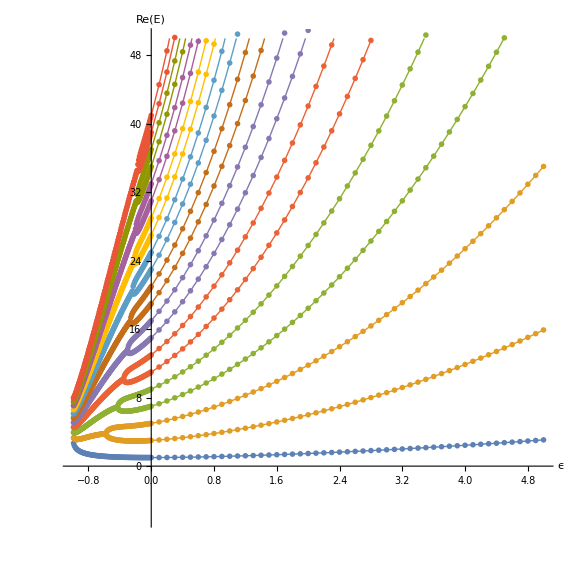

```mathematica
(*Traguem parts real i imaginaria*)
dataRe=Table[Map[{#[[1]],Re[#[[2]]]}&,res[[i]]],{i,Neig}];dataIm=Table[Map[{#[[1]],Im[#[[2]]]}&,res[[i]]],{i,Neig}];coloresDuo=Table[ColorData[97][1+Ceiling[(i-1)/2]],{i,Neig}];
(*Gràfic*)
ListPlot[dataRe,PlotRange->{{-1,5},{-6,50}},Joined->True,PlotMarkers->{●,2},AspectRatio->1,PlotStyle->Flatten[{Table[{Thick,coloresDuo[[i]]},{i,Neig}],Table[{Thick,coloresDuo[[i]],Dashed},{i,Neig}] },1],AxesLabel->{"ϵ","Re(E)"},PlotLabel->None,ImageSize->Large]
```

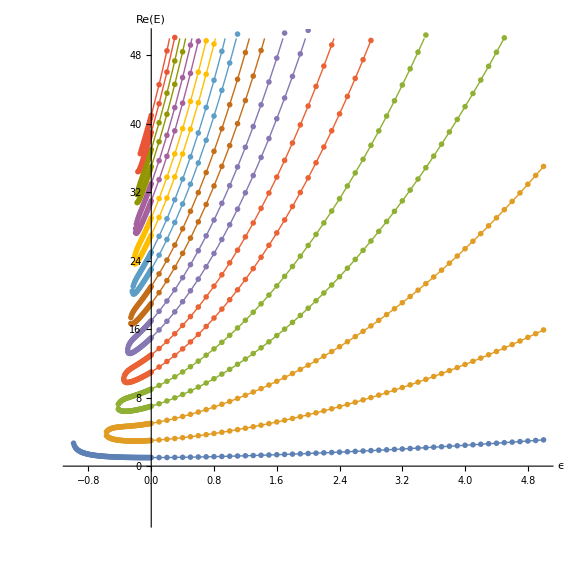

```mathematica
ListPlot[res,PlotRange->{{-1,5},{-6,50}},Joined->True,PlotMarkers->{●,1},AspectRatio->1,PlotStyle->Flatten[{Table[{Thick,coloresDuo[[i]]},{i,Neig}],Table[{Thick,coloresDuo[[i]],Dashed},{i,Neig}] },1],AxesLabel->{Style["ϵ",16],Style["Re(E)",14]},PlotLabel->None,ImageSize->Large]
```